```mathematica
<<SpinSin`
```

```mathematica
(*Parameters*)

(*our spins*)
spins={1/2,1/2};
(*exchange between spins*)
Jc1=-2;
(*exchanges between spin and conduction electrons*)
Jl=-10*{0.1,0.1,0.1,0.1};
(*their coordinates, A*)
spinsCoo={{0,0,0},{0,3,0},{3,0,0},{3,0,3}};
(*Fermi k vector, 1/A*)
kF=1;
(*DOS on Ef, ev^-1*)
rho=0.1;
(*kB*T, meV*)
kBT=0.01

n=Dimensions[spins][[1]];
mainJ=Sum[HeisLS[spins,{i,i+1},Jc1],{i,1,n-1}];
fieldZ=ZeemanLS[spins,1,{0.,0.,1.}];
fieldX=ZeemanLS[spins,1,{1.,0.,0.}];

sops=Table[SpinOpLS[spins,i],{i,1,n}];

ham = {mainJ+fieldZ};


confls={spins,ham,sops};
```

0.01

```mathematica
HH//MatrixForm
```

HH

```mathematica
PlanckNorm=0.6582;
PlanckNormInv = 1./PlanckNorm;

TensorMultiply[A_,B_,pairs_]:=Activate@TensorContract[Inactive[TensorProduct][A,B],pairs];

(*Acting of Renfield operator on density matrix*)
RedfieldRHSt[R_,dm_]:=TensorMultiply[R,dm,{{3,5},{4,6}}]

(*Right Hand Side part of time dependent QME *)
RHStd[ham_,R_,dm_]:=-ⅈ PlanckNormInv (ham.dm-dm.ham )+RedfieldRHSt[R,dm]

RungeKuttaStepDMRtd[dm_,ham_,redfield_,time_,step_]:=
Module[{k1,k2,k3,k4},
k1=RHStd[ham[time],redfield,dm];
k2=RHStd[ham[time+0.5*step],redfield,dm+k1 *step*0.5];
k3=RHStd[ham[time+0.5*step],redfield,dm+k2 *step*0.5];
k4=RHStd[ham[time+step],redfield,dm+k3 *step];
Return[1./6.(k1+2.0 k2+2.0 k3 + k4)];
]
```

```mathematica
BuildRedfieldOperator[
SysConfig_, (*={spin, ham, sops}*)
spinsCoo_,
KondoJRho_,
kFermi_,
kBT_,
SecularApproximation_:False
]:=Module[
{
Jrho=KondoJRho,
PlanckNorm=0.6582,
PlanckNormInv = 1./PlanckNorm,
StructFactor,
spin=SysConfig[[1]],
fullHam=SysConfig[[2]],
sops=SysConfig[[3]],
dim,
nspins
},
dim=Dimensions[fullHam[[1]]][[1]];
nspins=Dimensions[spin][[1]];

(*our spins*)
(*spins={1/2,1/2,1/2};*)
(*exchange between spins*)
(*Jc1=-2;*)
(*exchanges between spin and conduction electrons*)
(*Jl=-10*{0.1,0.1,0.1,0.1};*)
(*their coordinates, A*)
(*spinsCoo=0.3{{0,0,0},{0,3,0},{3,0,0},{3,0,3}};*)
(*Fermi k vector, 1/A*)
(*kF=1;*)
(*DOS on Ef, ev^-1*)
(*rho=0.1;*)
(*kB*T, meV*)
(*kBT=0.001*)
(*Planck Constant in ps*mEv*)

(*Spherical symmetrical structure factor*)
StructFactor=Table[Sinc[kFermi*Norm[spinsCoo[[l1]]-spinsCoo[[l2]]]]^2//N,{l1,1,nspins},{l2,1,nspins}];

(*Spherical symmetrical integral of bath correlator dependent on energy deltas*)
FF[d_,Temp_]:=If[d==0,Temp,If[Temp==0,If[d>0,d,0],d/(1-Exp[-d/Temp ])]];

(*Help function for conraction*)
TensorMultiply[A_,B_,pairs_]:=Activate@TensorContract[Inactive[TensorProduct][A,B],pairs];

(*transform to eigenbasis*)
esys=Sort[Transpose[Eigensystem[fullHam[[1]]]],#1[[1]]<#2[[1]]&];
U=SparseArray[Transpose[esys[[1;;,2]]]];

(*Eigenvalues (energies of unperturbed system)*)
evals=esys[[1;;,1]];

(*Static unperturbed diagonal Hamiltonian in eigenbasis*)
Hdiag=SparseArray[DiagonalMatrix[esys[[1;;,1]]]];

(*spin matrices in eigenbasis*)
sopsEig=Table[Chop[SparseArray[ConjugateTranspose[U].opc.U],1*^-11],{op,sops},{opc,op}];

(*Other perturbation operators in eigenbais*)
fullHamEig=Hdiag~Join~Table[Chop[SparseArray[ConjugateTranspose[U].op.U],1*^-11],{op, fullHam[[2;;]]}];

(*Lambda struct factor*)
LambdaSF=1./4.SparseArray[ParallelTable[
Chop[
Sum[
StructFactor[[i,j]]Jrho[[j]]Jrho[[i]]sopsEig[[i,a]][[n1,n2]] sopsEig[[j,a]][[m1,m2]]
,{i,1,nspins},{j,1,nspins},{a,1,3}]
,1*^-11]
,{n1,1,dim},{n2,1,dim},{m1,1,dim},{m2,1,dim}]];


(*Deltas of energies*)
Deltas=SparseArray[Table[evals[[n1]]-evals[[n2]],{n1,1,dim},{n2,1,dim}]];

Fdeltas=Map[FF[#,kBT]&,Deltas,{2}];

RR=SparseArray[{{{{0}}}},{dim,dim,dim,dim}];

Redfield=Pi PlanckNormInv  (-ReplacePart[RR,{n_,x_,m_,x_}:>Sum[LambdaSF[[n,npp,npp,m]]*Fdeltas[[m,npp]],{npp,1,dim}]]+
ReplacePart[RR,{n_,np_,m_,mp_}:>LambdaSF[[n,m,mp,np]]*Fdeltas[[m,n]]]-
ReplacePart[RR,{x_,np_,x_,mp_}:>Sum[LambdaSF[[mp,npp,npp,np]]*Fdeltas[[mp,npp]],{npp,1,dim}]]+
ReplacePart[RR,{n_,np_,m_,mp_}:>LambdaSF[[n,m,mp,np]]*Fdeltas[[mp,np]]]);

RedfieldSecular = If[SecularApproximation==True,
 SparseArray[Table[ 
ind=Keys[rule];
If[ 
Abs[Deltas[[ind[[1]],ind[[2]]]]-Deltas[[ind[[3]],ind[[4]]]]] < kBT,
rule,
ind->0
]
,{rule,ArrayRules[Redfield]}]]
,
Redfield
];



Return[
{
"SpinOpsEig"->sopsEig,
"FullHamEig"->fullHamEig,
"Redfield"->RedfieldSecular,
"U"->U
}
];
];
```

```mathematica
SpinDynamicRedfieldLS[
RedfieldConfig_,
SysConfig_,
ParNames_,
ParValList_,
TimeUnits_,
TimeStep_,
MaxTime_,
outEveryPS_,
Temp_:0,
numStates_:1,
tol_:0.05,
outtol_:0.1
]:=Module[
{
NumSteps=MaxTime/TimeStep,
NormTime=1,
PlanckPS=0.6582,
PlanckNorm=0.6582,
t,
λ,
initJ=SysConfig[[1]],
ham=SysConfig[[2]],
Sops=SysConfig[[3]],
bsize = Dimensions[SysConfig[[3,1]]][[1]],
en=0,
adtol=0,
outadtol,
done,
TimeArr,
Parameters,
U="U"/.RedfieldConfig,
redfield="Redfield"/.RedfieldConfig,
hamEig,
n=Dimensions[ham[[1]]][[1]]
},

adtol=tol/Sqrt[bsize];
outadtol=outtol/Sqrt[bsize];

(*If[Temp==0,
Return[
SpinDynamic[
SysConfig,
ParNames,
ParValList,
TimeUnits,
DampConst,
TimeStep,
NumSteps,
1]
],
None]
*)


progressBar[Dynamic[done],100];
SetSystemOptions["CatchMachineUnderflow" -> False];

If[TimeUnits=="FS",NormTime=1000];
PlanckNorm=PlanckPS*NormTime;

Clear[lt];

If[Dimensions[ParValList]≠{},
pdt=MaxTime/(Dimensions[ParValList][[2]]-1);
TimeArr=Table[pdt*(it-1),{it,1,Dimensions[ParValList][[2]]}];
Parameters=Map[Interpolation[Transpose[{TimeArr,#}]]&,ParValList];
,
Parameters={};
];

ParamsF[lt_]:=Map[#[lt]&,Parameters];

Print["Convert operators in eigenbasis"];

hamEig = Table[ConjugateTranspose[U].h.U,{h,ham}];

HAM[lt_]:=GetHam[hamEig,ParamsF[lt]];


(*Print["Solving eigensystem for initial state..."];
*)
(*initHam=GetHam[-hamEig,ParValList[[1;;,1]]];
*)
(*ES=Eigensystem[
GetHam[-ham,ParValList[[1;;,1]]],
numStates,Method->{"Arnoldi","Criteria"->"RealPart"}];

ests = -ES[[1]];
evec=ES[[2]];*)


Print["init density matrix"];

(*DM in eigenbasis (initially diagonal), chose eigenstate*)
dim=Dimensions[hamEig[[1]]][[1]];

dm=SparseArray[{{0}},{dim,dim}];

If[Temp==0,

dm[[numStates,numStates]]=1;,

(*Start density matrix*)
relEn=Table[en-ests[[1]],{en,ests[[1;;numStates]]}];
occup=Table[Exp[-en/Temp]//Re,{en, relEn}]//N;
Zsum=Sum[occ,{occ,occup}];

Table[
dm[[i,i]]=occup[[i]];
,{i,1,numStates}];

(*dm=1/Zsum * Sum[
occup[[i]] KroneckerProduct[
Conjugate[SparseArray[clean[evec[[i]],adtol]]],
SparseArray[clean[evec[[i]],adtol]]
]
,{i,1,numStates}];
*)
];


trace=Tr[dm];
dm=dm/trace;

Print["Occupation numbers: ",occup];


(*Time step*)
dt=TimeStep*NormTime;

(*Damping constant*)
(*λ=DampConst;*)


(*En={};*)
T={};
(*Sz={};
Sx={};
Sy={};*)
Bar={};

t=0;
DMs={};

done=0;
doneEvery=IntegerPart[NumSteps/100]+1;
doneCount=0;

saveCount=0;
saveEvery=IntegerPart[outEveryPS/dt];
If[saveEvery<1,saveEvery=1];

Print["Dynamic started..."];

calcPassed=False;

i=1;
dtpp=MaxTime/100.;
While[t<MaxTime-dt,


(*Hnum=GetHam[hamEig,ParValList[[1;;,i]]];*)

While[calcPassed==False,


(*Make step of RK with Redfield ME*)
dmn=dm + dt * RungeKuttaStepDMRtd[dm,HAM,redfield,t,dt]; (*RungeKuttaStepDMR[dm,TimeStep];*)

(*dmn=dm+dt * RungeKuttaStepDM[dm,Hnum,1./((1.+λ^2)PlanckNorm),λ,TimeStep];*)(*/( (1.+λ^2)PlanckNorm) (I comm-λ Commute[dm,comm]);*)

norm = Tr[dm];



If[Abs[norm-1.] < 0.0001,
calcPassed=True;
,
dt*=0.9;
Print["WARNING! Norm of wave function is not 1: ",norm,"! Decreasing step to: ",dt,"; Time: ",t];
calcPassed=False;
];


];


If[Abs[norm-1.]>0.00001,
dm=dmn/norm;
,
dm=dmn;
];

calcPassed=False;
t+=dt;

If[saveCount>=outEveryPS,
saveCount=0;
(*AppendTo[En,en];*)
AppendTo[T,t];
(*AppendTo[Bar,ParValList[[1;;,i]]];*)
AppendTo[DMs,dm];

];


saveCount+=dt;

If[doneCount >= dtpp,
 (*Print[done," % done "];*)
done = t/MaxTime * 100;
doneCount=doneCount-dtpp;
];
doneCount+=dt;


i++;
];


(*Sall={Sx,Sy,Sz};*)

(*Send=S;
Stot=Transpose[Sqrt[Re[Sx]^2+Re[Sy]^2+Re[Sz]^2]];*)
(*

Result={
T,
Bar,
(*Sall,*)
En,
ParNames,
TimeUnits,
n,
Psi
};
*)
Result={
"Time"-> T,
(*"Parameters"-> Bar,*)
(*"SpinComponents"-> Sall,
"AddObservables"->Transpose[AddObservables],*)
(*"Energy"-> En,*)
"ParamNames"-> ParNames,
"TimeUnits"-> TimeUnits,
"NumSpins"-> n,
"DensityMatrix" -> DMs,
"SpinOps"->Sops
};


Print["Done!"];

Return[Result];

]
```

```mathematica
res=BuildRedfieldOperator[
confls, (*={spin, ham, sops}*)
spinsCoo,
Jl*rho,
kF,
kBT,
False];
```

```mathematica
dt=0.1;
MaxTime = 100;

tdres=SpinDynamicRedfieldLS[
res,
confls,
0,
0,
"PS",
dt,
MaxTime,
0.1,
0,
2,
0.01,
0.01
];
```

%

SetSystemOptions::sysname: CatchMachineUnderflow is not a known SystemOption.

Convert operators in eigenbasis

init density matrix

Occupation numbers: occup

Dynamic started...

Done!

```mathematica
sopseig="SpinOpsEig"/.res;
```

```mathematica
dms="DensityMatrix"/.tdres;
```

```mathematica
sopseig
```

{{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]}}

```mathematica
sz=Table[Re[Tr[sopseig[[spin,3]].dm]],{spin,1,n},{dm,dms}];
(*s2=Table[Tr[sopseig[[2,3]].dm],{dm,dms}];*)
```

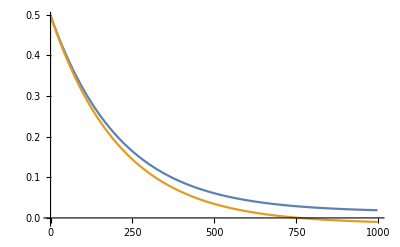

```mathematica
ListLinePlot[sz,PlotRange->All]
```

```mathematica
"Redfield"/.res//MatrixForm
```

((0. | 0. | -3.42722×10^-6 | 0.
0. | 0.0469439 | 0. | 0.
-3.42722×10^-6 | 0. | 0.0476044 | 0.
0. | 0. | 0. | 0.0483251) | (0. | -0.0235328 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0.000688562 | 0. | 0.
-0.0241523 | 0. | -0.000712176 | 0.) | (0. | 0. | -0.0241564 | 0.
0. | -1.50897×10^-6 | 0. | 0.
0.0238022 | 0. | 0.00138055 | 0.
0. | 0. | 0. | -1.57524×10^-6) | (0. | 0. | 0. | -0.0245653
-0.0234621 | 0. | -0.000681942 | 0.
0. | 0. | 0. | 0.000688562
0. | 0. | 0. | 0.)
(0. | 0. | 0. | -0.0241523
-0.0235328 | 0. | 0.000688562 | 0.
0. | 0. | 0. | -0.000712176
0. | 0. | 0. | 0.) | (2.7301×10^-173 | 0. | -2.25809×10^-8 | 0.
0. | -0.0469459 | 0. | 0.
-2.25809×10^-8 | 0. | 0.000705636 | 0.
0. | 0. | 0. | 0.) | (0. | 0. | 0. | -9.91827×10^-6
1.72494×10^-6 | 0. | -0.047689 | 0.
0. | 0. | 0. | 0.000695437
0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0482176
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(-1.11735×10^-177 | 0. | 0.0238022 | 0.
0. | -1.50897×10^-6 | 0. | 0.
-0.0241564 | 0. | 0.00138055 | 0.
0. | 0. | 0. | -1.57524×10^-6) | (0. | 1.72494×10^-6 | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.047689 | 0. | 0.
-9.91827×10^-6 | 0. | 0.000695437 | 0.) | (7.70587×10^-176 | 0. | 3.44987×10^-6 | 0.
0. | 1.96407×10^-6 | 0. | 0.
3.44987×10^-6 | 0. | -0.0483123 | 0.
0. | 0. | 0. | 0.00068582) | (0. | 0. | 0. | 1.72494×10^-6
-2.84042×10^-8 | 0. | 2.1104×10^-6 | 0.
0. | 0. | 0. | -0.0487214
0. | 0. | 0. | 0.)
(0. | -0.0234621 | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.000681942 | 0. | 0.
-0.0245653 | 0. | 0.000688562 | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.0482176 | 0. | 0.) | (0. | -2.84042×10^-8 | 0. | 0.
0. | 0. | 0. | 0.
0. | 2.1104×10^-6 | 0. | 0.
1.72494×10^-6 | 0. | -0.0487214 | 0.) | (2.57605×10^-178 | 0. | -7.22735×10^-11 | 0.
0. | 0. | 0. | 0.
-7.22735×10^-11 | 0. | 2.25849×10^-6 | 0.
0. | 0. | 0. | -0.0490109))

```mathematica
ham = {mainJ,fieldZ};


confls={spins,ham,sops};

res=BuildRedfieldOperator[
confls, (*={spin, ham, sops}*)
spinsCoo,
Jl*rho,
kF,
kBT,
False];
```

```mathematica
MaxTime = 10;
pdt=0.01;
dt=0.01;



BzF[t_]:=(*B0x (UnitStep[-t+5]UnitStep[t+10])*)B0x ⅇ^(-((t-t0)/Tw)^2)/(√π Tw);


parvalls={
(*Table[(BxF[t])/.{B0x->0,t0->0.05,Tw->0.02},{t,0,MaxTime,pdt}],
Table[(BzF[t])/.{B0z->1,t02->10,Tw->10},{t,0,MaxTime,pdt}]*)
Table[(BzF[t])/.{B0x->0,t0->10,Tw->1},{t,1,MaxTime,dt}]
(*Table[BzF[t]/.{B0z->2},{t,1,MaxTime,dt}]*)
};

tdres=SpinDynamicRedfieldLS[
res,
confls,
{Bz},
parvalls,
"PS",
dt,
MaxTime,
0.1,
0,
1,
0.01,
0.01
];
```

%

SetSystemOptions::sysname: CatchMachineUnderflow is not a known SystemOption.

Convert operators in eigenbasis

init density matrix

Occupation numbers: occup

Dynamic started...

Done!

```mathematica
sopseig="SpinOpsEig"/.res;
dms="DensityMatrix"/.tdres;
sz=Table[Re[Tr[sopseig[[spin,3]].dm]],{spin,1,n},{dm,dms}];
(*s2=Table[Tr[sopseig[[2,3]].dm],{dm,dms}];*)
```

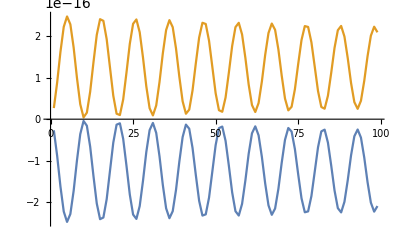

```mathematica
ListLinePlot[sz,PlotRange->All]
```

```mathematica
dms[[1]]//MatrixForm
```

(1.+1.81286×10^-52 ⅈ | 0.+0. ⅈ | -2.3855×10^-17+6.86081×10^-17 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 2.94071×10^-38+4.54709×10^-55 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-2.98188×10^-17-8.58127×10^-17 ⅈ | 0.+0. ⅈ | 6.6092×10^-33+8.8558×10^-50 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.94071×10^-38+4.54709×10^-55 ⅈ)

```mathematica
(*Parameters*)

(*our spins*)
spins={1/2,1/2};
(*exchange between spins*)
Jc1=-1;
(*exchanges between spin and conduction electrons*)
Jl=-50*{0.1,0.1,0.1,0.1};
(*their coordinates, A*)
spinsCoo={{0,0,0},{0,3,0},{3,0,0},{3,0,3}};
(*Fermi k vector, 1/A*)
kF=1;
(*DOS on Ef, ev^-1*)
rho=0.1;
(*kB*T, meV*)
kBT=0.01

n=Dimensions[spins][[1]];
mainJ=Sum[HeisLS[spins,{i,i+1},Jc1],{i,1,n-1}]+0ZeemanLS[spins,1,{0.,0.,1.}];
fieldZ=ZeemanLS[spins,1,{0.,0.,1.}];
fieldX=ZeemanLS[spins,1,{1.,0.,0.}];

sops=Table[SpinOpLS[spins,i],{i,1,n}];

ham = {mainJ,fieldZ,fieldX};


confls={spins,{GetHam[ham,{0,1}]},sops};
```

0.01

```mathematica
ham
```

{SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
confls={spins,ham,sops};

res=BuildRedfieldOperator[
confls, (*={spin, ham, sops}*)
spinsCoo,
Jl*rho,
kF,
kBT,
False];
```

```mathematica
rr="Redfield"/.res;
rr//MatrixForm
```

((-2.47152×10^-87 | 0. | 0. | 0.
0. | 0.595306 | 0. | 0.
0. | 0. | 0.595306 | 0.
0. | 0. | 0. | 0.595306) | (0. | -0.300643 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
-0.297653 | 0. | 0. | 0.) | (0. | 0. | -0.300643 | 0.
0. | 0. | 0. | 0.
0.297653 | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (0. | 0. | 0. | -0.300643
-0.297653 | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | -0.297653
-0.300643 | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (8.23841×10^-88 | 0. | 0. | 0.
0. | -0.598295 | 0. | 0.
0. | 0. | 0.00298973 | 0.
0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | -0.601285 | 0.
0. | 0. | 0. | 0.00298973
0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | -0.604275
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0.297653 | 0.
0. | 0. | 0. | 0.
-0.300643 | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.601285 | 0. | 0.
0. | 0. | 0.00298973 | 0.) | (8.23841×10^-88 | 0. | 0. | 0.
0. | 0.00298973 | 0. | 0.
0. | 0. | -0.601285 | 0.
0. | 0. | 0. | 0.00298973) | (0. | 0. | 0. | 0.
0. | 0. | 0.00298973 | 0.
0. | 0. | 0. | -0.601285
0. | 0. | 0. | 0.)
(0. | -0.297653 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
-0.300643 | 0. | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.604275 | 0. | 0.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0.00298973 | 0. | 0.
0. | 0. | -0.601285 | 0.) | (8.23841×10^-88 | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0.00298973 | 0.
0. | 0. | 0. | -0.598295))

```mathematica
MaxTime = 100;
pdt=0.01;
dt=0.01;



SlowStep[t_]:=If[t<-1,-1,If[t≤1&&t≥-1,t,1]];
BzF[t_]:=B0z SlowStep[(t-t02)];
BxF[t_]:=(*B0x (UnitStep[-t+5]UnitStep[t+10])*)B0x ⅇ^(-((t-t0)/Tw)^2)/(√π Tw);


parvalls={

Table[(BzF[t])/.{B0z->1,t02->10,Tw->1},{t,0,MaxTime,pdt}],
Table[(BxF[t])/.{B0x->1,t0->15,Tw->1},{t,0,MaxTime,pdt}]

(*Table[(BxF[t])/.{B0x->10,t0->10,Tw->1},{t,1,MaxTime,dt}]*)
(*Table[BzF[t]/.{B0z->2},{t,1,MaxTime,dt}]*)
};

tdres=SpinDynamicRedfieldLS[
res,
confls,
{Bz,Bx},
parvalls,
"PS",
dt,
MaxTime,
0.05,
0,
1,
0.001,
0.001
];
```

General::munfl: 3.01653×10^-308 0.56419 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.624] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.157] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

%

SetSystemOptions::sysname: CatchMachineUnderflow is not a known SystemOption.

Convert operators in eigenbasis

init density matrix

Occupation numbers: occup

Dynamic started...

Done!

```mathematica
sopseig="SpinOpsEig"/.res;
dms="DensityMatrix"/.tdres;


(*s2=Table[Tr[sopseig[[2,3]].dm],{dm,dms}];*)
```

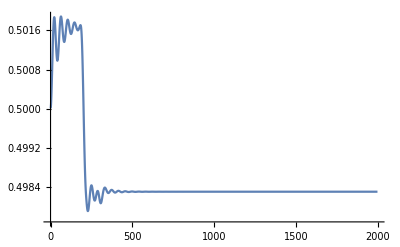

```mathematica
En=Table[Re[Tr[ham.dm]],{dm,dms}];
ListLinePlot[En,PlotRange->All]
```

```mathematica
En[[1]]
En[[400]]
```

0.500014

0.498302

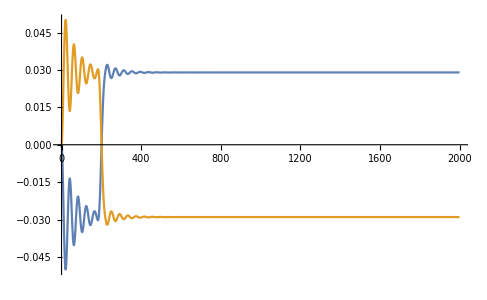

```mathematica
sz=Table[Re[Tr[sopseig[[spin,3]].dm]],{spin,1,n},{dm,dms}];
ListLinePlot[sz,PlotRange->All]
```

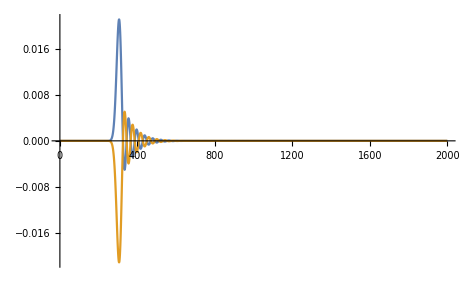

```mathematica
sx=Table[Re[Tr[sopseig[[spin,1]].dm]],{spin,1,n},{dm,dms}];
ListLinePlot[sx,PlotRange->All]
```

```mathematica
Chop[dms[[999]],10^-5]
```

SparseArray[…]

```mathematica
ev=Eigenvalues[dms[[1]]]
```

{1.,1.25539×10^-8,6.37122×10^-11,6.37122×10^-11}

```mathematica
Dot[ev,Log[ev]]/4
```

-6.10172×10^-8

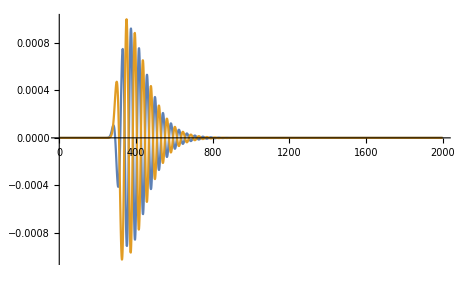

```mathematica
sy=Table[Re[Tr[sopseig[[spin,2]].dm]],{spin,1,n},{dm,dms}];
ListLinePlot[sy,PlotRange->All]
```

```mathematica
(*dmsf=Table[ 
Flatten[
Table[
If[i==j,
0,
dm[[i,j]]
],
{i,1,4},{j,1,4}
] 
]
,{dm,dms[[1;;]]}]//Transpose;*)

dmsf=Table[ 
{dm[[1,2]],dm[[1,3]],dm[[2,3]],dm[[1,4]],dm[[2,4]]}
,{dm,dms[[1;;]]}]//Transpose;
```

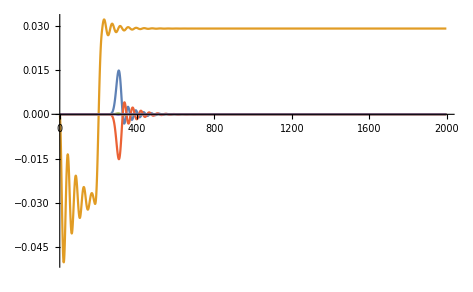

```mathematica
ListLinePlot[Re[dmsf],PlotRange->All]
```

```mathematica
Dimensions[dmsf]
```

{5,1999}

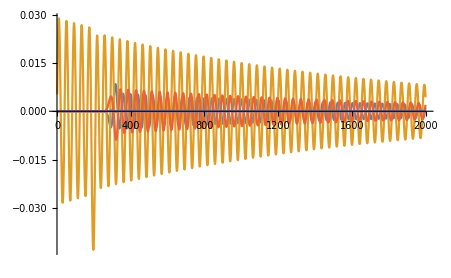

```mathematica
ListLinePlot[Im[dmsf],PlotRange->All]
```

```mathematica
dmsf[[1;;,1]]//Dimensions
```

{5}

```mathematica
dmsdiag=Table[ 
Flatten[
Table[
dm[[i,i]],
{i,1,9}
] 
]
,{dm,dms[[1;;]]}]//Transpose;
```

Part::partw: Part 5 of «1» does not exist.

Part::partw: Part 6 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

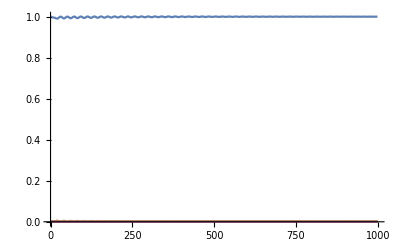

```mathematica
ListLinePlot[Re[dmsdiag],PlotRange->All]
```

```mathematica
ListLinePlot[Im[dmsdiag],PlotRange->All]
```

Part::partw: Part 5 of «1» does not exist.

Part::partw: Part 5 of {{0.999972-1.59856×10^-26 ⅈ,7.556×10^-102-1.1306×10^-100 ⅈ,-0.000480395+0.00525403 ⅈ,-7.21809×10^-102+1.13104×10^-100 ⅈ},{7.556×10^-102+1.1306×10^-100 ⅈ,«2»,«1»},«1»,{-7.21809×10^-102-1.13104×10^-100 ⅈ,-1.28461×10^-200-3.85531×10^-203 ⅈ,5.97952×10^-103+1.64114×10^-104 ⅈ,6.66764×10^-11-8.02488×10^-29 ⅈ}} does not exist.

Part::partw: Part 5 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
vv=Eigenvectors[{{a,b},{Conjugate[b],d}}]//FullSimplify
```

{{-(-a+d+√((a-d)^2+4 b Conjugate[b]))/(2 Conjugate[b]),1},{(a-d+√((a-d)^2+4 b Conjugate[b]))/(2 Conjugate[b]),1}}

```mathematica
Normalize[vv[[1]]]
```

{-(-a+d+√((a-d)^2+4 b Conjugate[b]))/(2 √(1+1/4 Abs[(-a+d+√((a-d)^2+4 b Conjugate[b]))/Conjugate[b]]^2) Conjugate[b]),1/(√(1+1/4 Abs[(-a+d+√((a-d)^2+4 b Conjugate[b]))/Conjugate[b]]^2))}

```mathematica
digamma
```

```mathematica
PolyGamma[1,x]
```

PolyGamma[1,x]

```mathematica
EulerGamma
```

```mathematica
4-0.627
```

3.373